```mathematica
a = 1;
J  = 1;

(*f function*)
f[N_] :=Module[{n, kx, ky, a},
a =1;
n = Range[0, N-1];
kx= (2 * Pi* n)/N ;
ky = Table[0, {N}, {N}];
Do[
ky[[i+1, j+1]]=((4*Pi*n[[j+1]]/(N*a))-(2*Pi*n[[i+1]]/N))*(1/Sqrt[3]), {i, 0, N-1},{j, 0, N-1}
];
Return[{kx, ky}]
]

(*Curly E*)
epsilon[kx_,ky_,X_,Y_,mu_,J1_]:=Module[{e1,e2,Ek},
e1=-8*X*J*(Cos[kx*a]+Cos[(kx*a/2)+(ky*Sqrt[3]*a/2)]+Cos[(kx*a/2)-(ky*Sqrt[3]*a/2)]);
e2=-8*Y*J1*(Cos[ky*a*Sqrt[3]]+Cos[(3*kx*a/2)-(ky*Sqrt[3]*a/2)]+Cos[(-3*kx*a/2)-(ky*Sqrt[3]*a/2)]);
Ek=e1+e2;
Return[Ek-mu];
]

(*Fermi function *)
fermi[ek_,T_]:=1/(Exp[ek/T]+1)
```

```mathematica
(* Q_grid for external momenta along GMKG path *)
Qgrid[N_]:=Module[{K, GM, MK, KG, GMKG, kx},
K = f[N];
kx = K[[1]];
kx = Insert[kx, Pi,1];
kx = Insert[kx, 4*Pi/3,1];

GM = {};
MK = {};
KG  = {};

GM = Table[
If[(i>0 && i<Pi)|| i == Pi || i==0 ,
{i, i/Sqrt[3]}, Nothing],{i,kx }
];

MK = Table[
If[(i>Pi && i< 4*Pi/3) || i == 4*Pi/3,
{i, ((4*Pi/Sqrt[3])-(Sqrt[3]*i))},Nothing],{i,kx}
];

KG = Table[
If[(i>0 && i<4*Pi/3 ), {i,0}, Nothing],{i,kx}
];
GM = SortBy[GM, First];
MK  = SortBy[MK, First];
KG   = SortBy[KG, First];
GMKG = Join[GM, MK, Reverse[KG]];

Return[GMKG];
]

(*Real_integrand*)
realintegrand[px_, py_, q_, ratio_, sol_, T_]:=Module[{qx,qy,X,Y,mu, J1, b, Ep,Epq,fp, fpq, ans},
qx = q[[1]];
qy=  q[[2]];
X   = sol[[1]];
Y   = sol[[2]];
mu = sol[[3]];
J1  = ratio;
b = 1/T;

If[(qx ==0 && qy ==0 ),
     Ep = epsilon[px, py, X, Y, mu, J1];
     ans = b*Exp[b*Ep]*(fermi[Ep,T])^2;
Return[Re[ans]]
];

Ep = epsilon[px, py, X, Y, mu, J1];
Epq = epsilon[px+qx, py+qy, X, Y, mu, J1];fp   = fermi[Ep, T];
fpq = fermi[Epq, T];
ans = (fp - fpq)/(Ep - Epq);
 Return[Re[-ans]]
]

(*Integration*)
Integration[q_, ratio_, sol_, T_]:=Module[{A},
A = NIntegrate[
realintegrand[px, py, q, ratio, sol, T],{px,0, 2*Pi},{py, 0, 4*Pi/Sqrt[3]}];
A= (A*Sqrt[3])/(8*(Pi)^2);
Return[A]
]

(*J(q)*)
V[ratio_, q_] :=Module[{NN, NNN, ans},
qx = q[[1]];
qy  = q[[2]];
NN = Exp[I*qx]+Exp[I*(qx/2 + qy*Sqrt[3]/2)]+Exp[I*(qx/2 - qy*Sqrt[3]/2)];
NNN = Exp[I*qy*Sqrt[3]]+Exp[I*(3*qx/2-qy*Sqrt[3]/2)]+Exp[I*(-3*qx/2-qy*Sqrt[3]/2)];
ans = NN + ratio*NNN;
Return[ans];
]

(* Data for Chi_0 *)
Datachi0[qn_,ratio_, sol_, T_]:=Module[{results, Q},
results = {};
Q  = Qgrid[qn];
results = Table[{i,Integration[i,ratio, sol, T]},{i,Q}];
Return[results]
]

(* Data for full Chi *)
Datachi[qn_, ratio_, sol_, T_]:=Module[{results, Q },
results = {};
Q  = Qgrid[qn];
results = Table[{i,Re[(Integration[i, ratio, sol, T])/(1+(Integration[i,ratio, sol, T]  * V[ratio, i]))]},{i,Q}];
Return[results];
]

(* Data for V(q) *)
DataV[qn_, ratio_]:=Module[{results, Q},
results = {};
Q = Qgrid[qn];
results = Table[{i, V[ratio, i]},{i,Q}];
Return[Re[results]];
]

(* Data for multi Chi *)
Dataprod[qn_, ratio_, sol_, T_]:=Module[{results, Q },
results = {};
Q  = Qgrid[qn];
results = Table[{i,Re[Integration[i,ratio, sol, T]  * V[ratio, i]]},{i,Q}];
Return[results];
]

(*Plotter2D for Chi0*)
Plotterchi0[data_, qn_]:=Module[{Q, Mindex, Kindex, Gindex, D, Ndata},
Q =Qgrid[qn];
D = Flatten[data, 0];
Ndata =D/. {q_, rest_} :>{First@First@Position[Q,q],rest};
Mindex = First@First@Position[Q,{Pi, Pi/Sqrt[3]}];
Kindex  = First@First@Position[Q,{4*Pi/3, 0}];
Gindex  = First@Position[Q,{0, 0}];
Return[ListLinePlot[Ndata,
AxesLabel->{"Path",Subscript[χ,0]},GridLines->Automatic,
Ticks -> {{{2, "Г"},{Mindex, "M"}, {Kindex, "K"}, {Length[Q], "Г"}}, Automatic}
]
]
]

(*Plotter2D for V*)
PlotterV[data_, qn_]:=Module[{Q, Mindex, Kindex, Gindex, D, Ndata},
Q =Qgrid[qn];
D = Flatten[data, 0];
Ndata =D /. {q_, rest_} :>{First@First@Position[Q,q],rest};
Mindex = First@First@Position[Q,{Pi, Pi/Sqrt[3]}];
Kindex  = First@First@Position[Q,{4*Pi/3, 0}];
Gindex  = First@Position[Q,{0, 0}];
Return[ListLinePlot[Ndata,
AxesLabel->{"Path","J(q)"},GridLines->Automatic,
Ticks -> {{{2, "Г"},{Mindex, "M"}, {Kindex, "K"}, {Length[Q], "Г"}}, Automatic}
]
]
]

(*Plotter for FullChi*)
Plotterchi[data_, qn_]:=Module[{Q, Mindex, Kindex, Gindex, secval, min, max, D, Ndata},
Q =Qgrid[qn];
D = Flatten[data, 0];
Ndata =D/. {q_, rest_} :>{First@First@Position[Q,q],rest};
Mindex = First@First@Position[Q,{Pi, Pi/Sqrt[3]}];
Kindex  = First@First@Position[Q,{4*Pi/3, 0}];
Gindex  = First@Position[Q,{0, 0}];
secval =data[[All,2]];
min = Min[secval];
max = Max[secval];
Return[ListLinePlot[Ndata,PlotRange->{Automatic,{min,max}},
AxesLabel->{"Path","χ",},GridLines->Automatic,
Ticks -> {{{2, "Г"},{Mindex, "M"}, {Kindex, "K"}, {Length[Q], "Г"}}, Automatic}
]
]
]

(*Converter*)
convert[data_, qn_]:=Module[{Ndata, Q, D},
Q =Qgrid[qn];
D = Flatten[data, 0];
Ndata =D/. {q_, rest_} :>{First@First@Position[Q,q],rest};
Return[Ndata]
]
```

Done

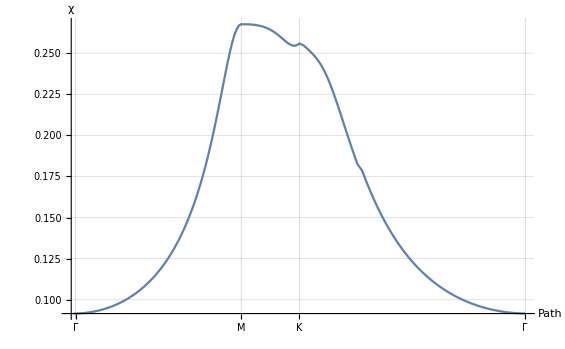

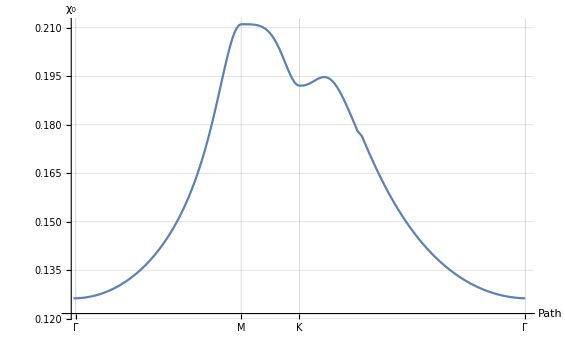

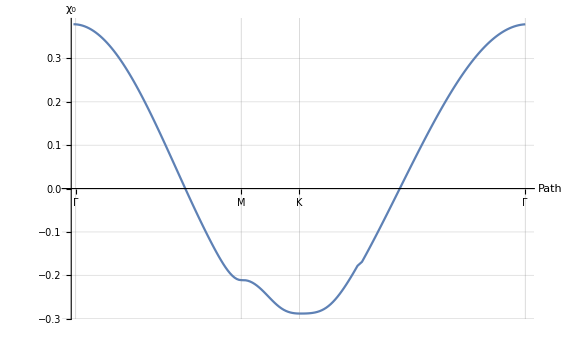

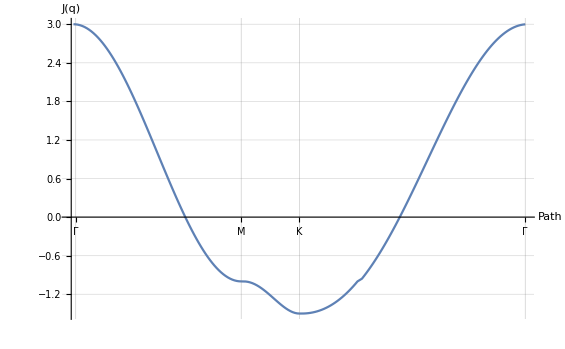

```mathematica
(* J1 = 0 *)
chidata = Datachi[150,0,{0.1502, 0.032, -1.024} , 0.2];
Print["Done"]
c0data = Datachi0[150,0,{0.1502, 0.032, -1.024} , 0.2];
dmulti = Dataprod[150,0,{0.1502, 0.032, -1.024} , 0.2];

Plotterchi[chidata, 150]
Plotterchi0[c0data, 150]
Plotterchi0[dmulti, 150]
vdata=DataV[150, 0];
PlotterV[vdata, 150]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,5.61838}. NIntegrate obtained 8.08009 and 0.000160678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,5.61838}. NIntegrate obtained 8.08009 and 0.000160678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,5.61838}. NIntegrate obtained 8.08009 and 0.000160678 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,5.61838}. NIntegrate obtained 8.08009 and 0.000160678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,5.61838}. NIntegrate obtained 8.08009 and 0.000160678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,5.61838}. NIntegrate obtained 8.08009 and 0.000160678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,5.61838}. NIntegrate obtained 8.08009 and 0.000160678 for the integral and error estimates.

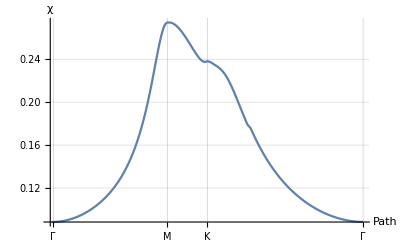

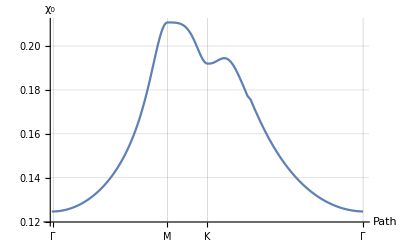

product

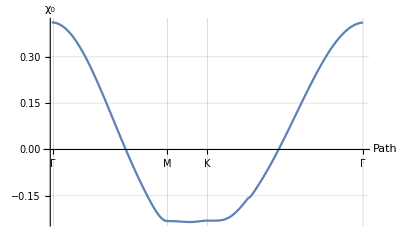

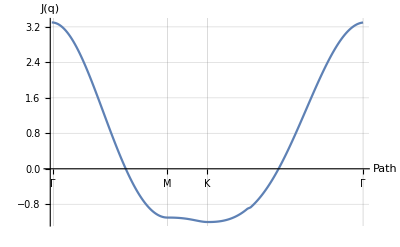

```mathematica
(* J1 = 0.1*)
chidata1 = Datachi[150,0.1,{0.15026978,0.03207748,-0.99771808} , 0.2];
Print["Done"]
c0data1 = Datachi0[150,0.1,{0.15026978,0.03207748,-0.99771808} , 0.2];
dmulti1 = Dataprod[150,0.1,{0.15026978,0.03207748,-0.99771808} , 0.2];

Plotterchi[chidata1, 150]
Plotterchi0[c0data1, 150]
Print[product]
Plotterchi0[dmulti1, 150]
PlotterV[vdata1, 150]
```

Done

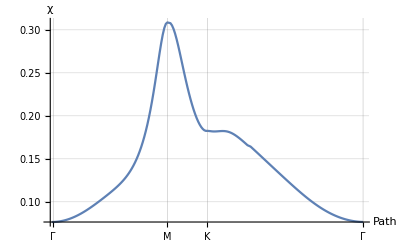

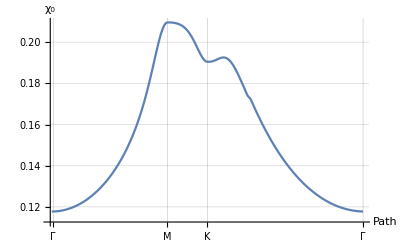

Prod

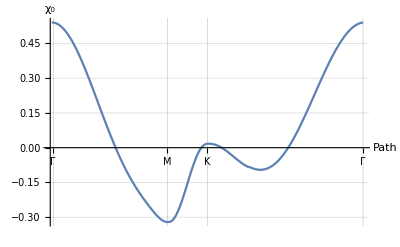

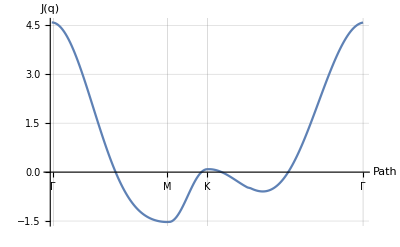

```mathematica
(* J1 = 0.53*)
chidata2 = Datachi[150,0.53,{0.15049688,0.03229799,-0.88845523} , 0.2];
Print["Done"]
c0data2 = Datachi0[150,0.53,{0.15049688,0.03229799,-0.88845523} , 0.2];
dmulti2 = Dataprod[150,0.53,{0.15049688,0.03229799,-0.88845523} , 0.2];

Plotterchi[chidata2, 150]
Plotterchi0[c0data2, 150]
Print[Prod]
Plotterchi0[dmulti2, 150]
vdata2=DataV[150, 0.53];
PlotterV[vdata2, 150]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.13359}. NIntegrate obtained 7.83797 and 0.0000915586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.13359}. NIntegrate obtained 7.83797 and 0.0000915586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.13359}. NIntegrate obtained 7.83797 and 0.0000915586 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.13359}. NIntegrate obtained 7.83797 and 0.0000915586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.13359}. NIntegrate obtained 7.83797 and 0.0000915586 for the integral and error estimates.

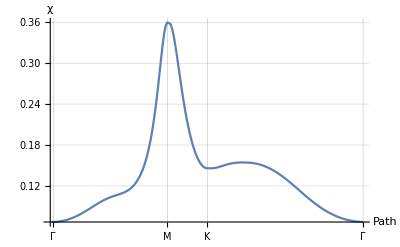

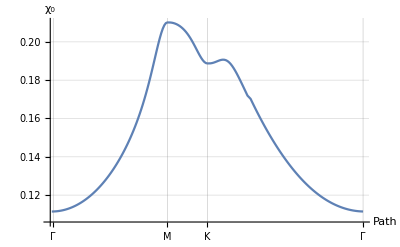

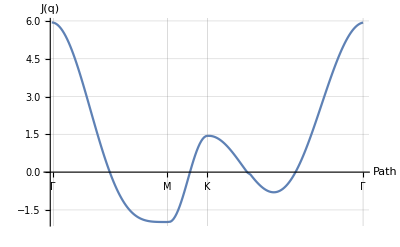

```mathematica
(* J1 = 0.98*)
chidata3 = Datachi[150,0.98,{0.15066678,0.03249723,-0.77450274} , 0.2];
Print["Done"]
c0data3 = Datachi0[150,0.98,{0.15066678,0.03249723,-0.77450274} , 0.2];
Plotterchi[chidata3, 150]
Plotterchi0[c0data3, 150]
vdata3=DataV[150, 0.98];
PlotterV[vdata3, 150]

dmulti2 = Dataprod[150,0.98,{0.15066678,0.03249723,-0.77450274} , 0.2];
Plotterchi0[dmulti2, 150]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.13359}. NIntegrate obtained 7.83797 and 0.0000915586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.13359}. NIntegrate obtained 7.83797 and 0.0000915586 for the integral and error estimates.

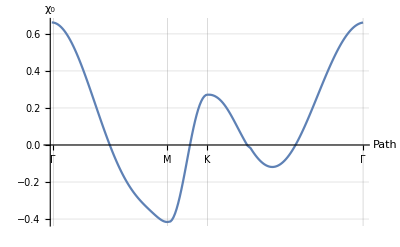

```mathematica
dmulti3 = Dataprod[150,0.98,{0.15066678,0.03249723,-0.77450274} , 0.2];
Plotterchi0[dmulti3, 150]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

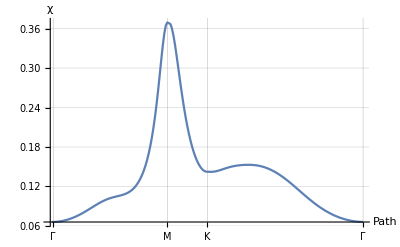

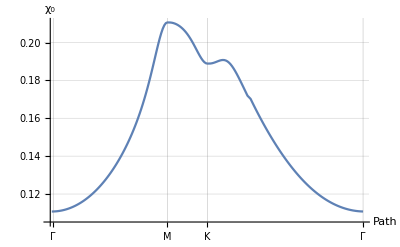

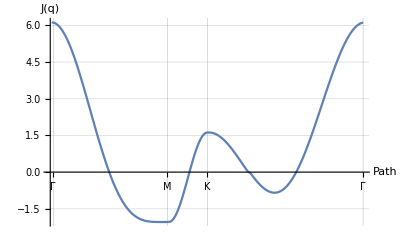

```mathematica
(* J1 = 1.04*)
chidata4 = Datachi[150,1.04,{0.15068688,0.03252717,-0.75711826} , 0.2];
Print["Done"]
c0data4 = Datachi0[150,1.04,{0.15068688,0.03252717,-0.75711826} , 0.2];
Plotterchi[chidata4, 150]
Plotterchi0[c0data4, 150]
vdata4=DataV[150, 1.04];
PlotterV[vdata4, 150]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.22861}. NIntegrate obtained 6.03188 and 0.00123773 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.22861}. NIntegrate obtained 6.03188 and 0.00123773 for the integral and error estimates.

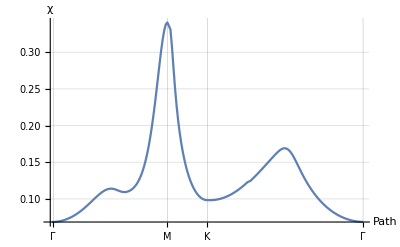

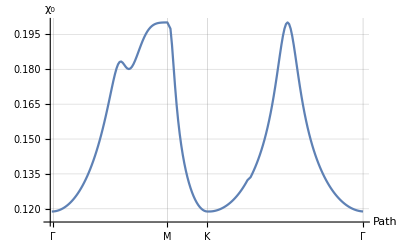

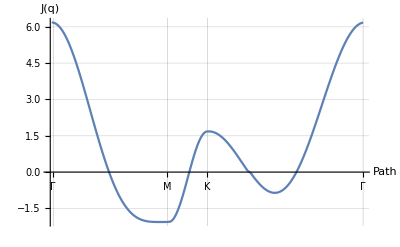

```mathematica
(* J1 = 1.06*)
chidata5 = Datachi[150,1.06,{5.83714749*10^(-09),0.150472383,-1.08577791} , 0.2];
Print["Done"]
c0data5 = Datachi0[150,1.06,{5.83714749*10^(-09),0.150472383,-1.08577791} , 0.2];
Plotterchi[chidata5, 150]
Plotterchi0[c0data5, 150]
vdata5=DataV[150, 1.06];
PlotterV[vdata5, 150]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.22861}. NIntegrate obtained 6.03188 and 0.00123773 for the integral and error estimates.

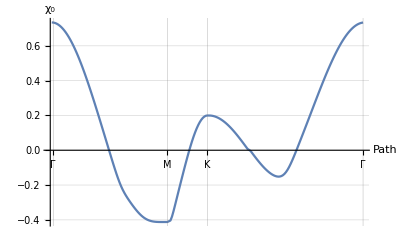

```mathematica
dmulti4 = Dataprod[150,1.06,{5.83714749*10^(-09),0.150472383,-1.08577791} , 0.2];
Plotterchi0[dmulti4, 150]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.23846}. NIntegrate obtained 5.80232 and 0.000507345 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in py near {px,py} = {5.79349,1.23846}. NIntegrate obtained 5.80232 and 0.000507345 for the integral and error estimates.

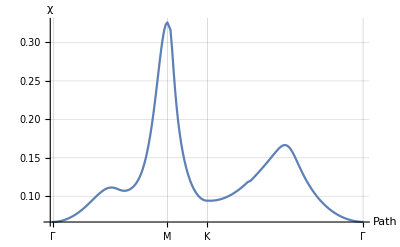

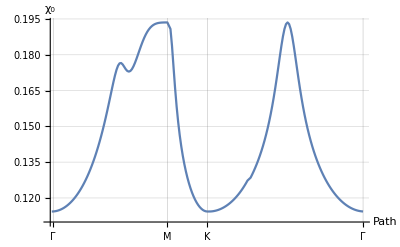

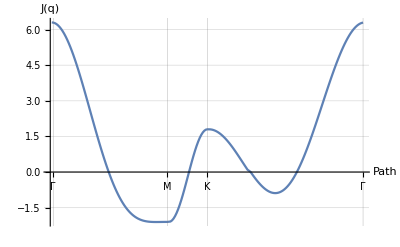

```mathematica
(* J1 = 1.1*)
chidata6 = Datachi[150,1.1,{2.7694538*10^(-08), 0.15062609,-1.1265610} , 0.2];
Print["Done"]
c0data6 = Datachi0[150,1.1,{2.7694538*10^(-08), 0.15062609,-1.1265610} , 0.2];
Plotterchi[chidata6, 150]
Plotterchi0[c0data6, 150]
vdata6=DataV[150, 1.1];
PlotterV[vdata6, 150]
```

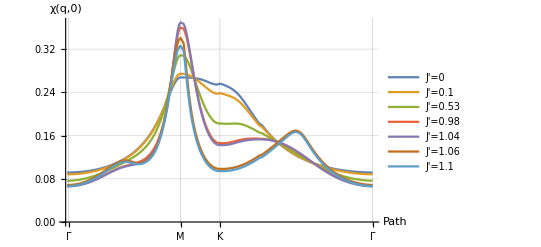

```mathematica
Q = Qgrid[150];
Mindex = First@First@Position[Q,{Pi, Pi/Sqrt[3]}];
Kindex  = First@First@Position[Q,{4*Pi/3, 0}];
Gindex  = First@Position[Q,{0, 0}];
A = ColorData["DarkRainbow"];
ListLinePlot[{convert[chidata,150],convert[chidata1,150], convert[chidata2,150], convert[chidata3,150], convert[chidata4,150], convert[chidata5,150],convert[chidata6,150]  },
PlotLegends->{"J'=0", "J'=0.1","J'=0.53", "J'=0.98", "J'=1.04","J'=1.06", "J'=1.1"},AxesLabel->{"Path","χ(q,0)",},GridLines->Automatic,
Ticks -> {{{2, "Г"},{Mindex, "M"}, {Kindex, "K"}, {Length[Q], "Г"}}, Automatic}]
```

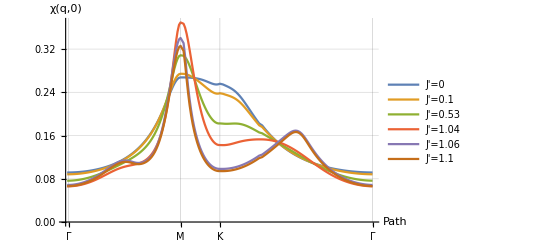

```mathematica
Q = Qgrid[150];
Mindex = First@First@Position[Q,{Pi, Pi/Sqrt[3]}];
Kindex  = First@First@Position[Q,{4*Pi/3, 0}];
Gindex  = First@Position[Q,{0, 0}];
A = ColorData["DarkRainbow"];
ListLinePlot[{convert[chidata,150],convert[chidata1,150], convert[chidata2,150],convert[chidata4,150], convert[chidata5,150],convert[chidata6,150]  },
PlotLegends->{"J'=0", "J'=0.1","J'=0.53","J'=1.04","J'=1.06", "J'=1.1"},AxesLabel->{"Path","χ(q,0)",},GridLines->Automatic,
Ticks -> {{{2, "Г"},{Mindex, "M"}, {Kindex, "K"}, {Length[Q], "Г"}}, Automatic}]
```

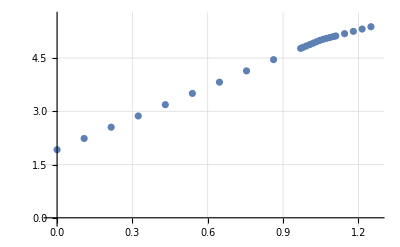

```mathematica
(* Avg Energy *) 
Eng = {19170.7068931674,22341.218927945,25511.9478152489,28682.831923869,31853.9120922086,35025.1661058517,38196.5955127633,41368.2584745327,44540.4312997417,47712.648557491,48006.9952135862,48399.4441592798,48791.9063365489,49184.3711922938,49576.8387902118,49969.3157876827,50279.7818700442,50526.6171300674,50773.5619744742,51020.6204191991,51205.9797564286,51855.2091309153,52505.0736737425,53155.5460930493,53806.5331309665};
xaxis = {0.0,0.107777777777778,0.215555555555556,0.323333333333333,0.431111111111111,0.538888888888889,0.646666666666667,0.754444444444444,0.862222222222222,0.97,0.98,0.993333333333333,1.00666666666667,1.02,1.03333333333333,1.04666666666667,1.06,1.07333333333333,1.08666666666667,1.1,1.11,1.145,1.18,1.215,1.25};
Edata = Transpose[{xaxis, Eng/(100)^2}];
ListPlot[Edata, GridLines->Automatic]
```